## Load packages and global definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../../Mathematica_packages/QMB.wl"]
Get["../../Mathematica_packages/Chaometer.wl"]
```

## Closed XXZ

```mathematica
L=9;(* number of spins *)
Δ=1.;(* anisotropy *)
```

Compute eigenvalues and eigenvectors of Hamiltonian:

```mathematica
{eigenvalsH,eigenvecsH}=Transpose[Sort[Transpose[Chop[Eigensystem[ClosedXXZHamiltonian[L,Δ]]]]]];
```

Define an initial random state for the environment (L-1 left-most spins in the chain):

```mathematica
ψE=RandomChainProductState[L-1];
```

Compute the superoperator for 0<=t<=50 (Δt=0.1) for every initial environmental state in ψE:

```mathematica
t=Power[10,Range[-2,2,0.05]];
```

```mathematica
{t0,tf,Δt}={0,10,0.2};
t=Power[10,Range[-2,2,0.05]];
AbsoluteTiming[superoperators=Chop[Superoperator[#,ψE,eigenvalsH,eigenvecsH,L]]&/@t;]
```

{42.53,Null}

```mathematica
chois=1/2*Reshuffle/@superoperators;
```

```mathematica
choiPurities=Chop[Purity/@chois];
```

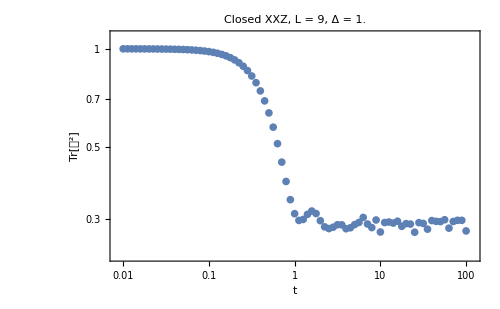

```mathematica
ListLogLogPlot[Transpose[{t,choiPurities}],
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->21],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,19],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Closed XXZ, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>", "<>ToString[TraditionalForm[HoldForm[Δ]]]<>" = "<>ToString[Δ],
LabelStyle->Directive[Black,FontSize->17]
]
```

```mathematica
myTicksXBelow=Join[Table[{10.^i,Superscript[10,i],{0.015,0}},{i,-2,2}](*major ticks*),Flatten[Table[{10^i+j*10.^(i),"",{.005,0}},{i,-2,1},{j,1,8}],1](*minor ticks*)]
```

{{0.01,10^-2,{0.015,0}},{0.1,10^-1,{0.015,0}},{1.,10^0,{0.015,0}},{10.,10^1,{0.015,0}},{100.,10^2,{0.015,0}},{0.02,,{0.005,0}},{0.03,,{0.005,0}},{0.04,,{0.005,0}},{0.05,,{0.005,0}},{0.06,,{0.005,0}},{0.07,,{0.005,0}},{0.08,,{0.005,0}},{0.09,,{0.005,0}},{0.2,,{0.005,0}},{0.3,,{0.005,0}},{0.4,,{0.005,0}},{0.5,,{0.005,0}},{0.6,,{0.005,0}},{0.7,,{0.005,0}},{0.8,,{0.005,0}},{0.9,,{0.005,0}},{2.,,{0.005,0}},{3.,,{0.005,0}},{4.,,{0.005,0}},{5.,,{0.005,0}},{6.,,{0.005,0}},{7.,,{0.005,0}},{8.,,{0.005,0}},{9.,,{0.005,0}},{20.,,{0.005,0}},{30.,,{0.005,0}},{40.,,{0.005,0}},{50.,,{0.005,0}},{60.,,{0.005,0}},{70.,,{0.005,0}},{80.,,{0.005,0}},{90.,,{0.005,0}}}

```mathematica
myTicksXAbove=Join[Table[{10.^i,"",{0.015,0}},{i,-2,2}](*major ticks*),Flatten[Table[{10^i+j*10.^(i),"",{.005,0}},{i,-2,1},{j,1,8}],1](*minor ticks*)]
```

{{0.01,,{0.015,0}},{0.1,,{0.015,0}},{1.,,{0.015,0}},{10.,,{0.015,0}},{100.,,{0.015,0}},{0.02,,{0.005,0}},{0.03,,{0.005,0}},{0.04,,{0.005,0}},{0.05,,{0.005,0}},{0.06,,{0.005,0}},{0.07,,{0.005,0}},{0.08,,{0.005,0}},{0.09,,{0.005,0}},{0.2,,{0.005,0}},{0.3,,{0.005,0}},{0.4,,{0.005,0}},{0.5,,{0.005,0}},{0.6,,{0.005,0}},{0.7,,{0.005,0}},{0.8,,{0.005,0}},{0.9,,{0.005,0}},{2.,,{0.005,0}},{3.,,{0.005,0}},{4.,,{0.005,0}},{5.,,{0.005,0}},{6.,,{0.005,0}},{7.,,{0.005,0}},{8.,,{0.005,0}},{9.,,{0.005,0}},{20.,,{0.005,0}},{30.,,{0.005,0}},{40.,,{0.005,0}},{50.,,{0.005,0}},{60.,,{0.005,0}},{70.,,{0.005,0}},{80.,,{0.005,0}},{90.,,{0.005,0}}}

```mathematica
myTicksYLeft=Join[Table[{i,NumberForm[i,{3,2}],{.015,0}},{i,0.25,1,0.15}],Table[{i,"",{0.005,0}},{i,0.25,1,0.05}]]
```

{{0.25,0.25,{0.015,0}},{0.4,0.40,{0.015,0}},{0.55,0.55,{0.015,0}},{0.7,0.70,{0.015,0}},{0.85,0.85,{0.015,0}},{1.,1.00,{0.015,0}},{0.25,,{0.005,0}},{0.3,,{0.005,0}},{0.35,,{0.005,0}},{0.4,,{0.005,0}},{0.45,,{0.005,0}},{0.5,,{0.005,0}},{0.55,,{0.005,0}},{0.6,,{0.005,0}},{0.65,,{0.005,0}},{0.7,,{0.005,0}},{0.75,,{0.005,0}},{0.8,,{0.005,0}},{0.85,,{0.005,0}},{0.9,,{0.005,0}},{0.95,,{0.005,0}},{1.,,{0.005,0}}}

```mathematica
myTicksYRight=Join[Table[{i,"",{.015,0}},{i,0.25,1,0.15}],Table[{i,"",{0.005,0}},{i,0.25,1,0.05}]]
```

{{0.25,,{0.015,0}},{0.4,,{0.015,0}},{0.55,,{0.015,0}},{0.7,,{0.015,0}},{0.85,,{0.015,0}},{1.,,{0.015,0}},{0.25,,{0.005,0}},{0.3,,{0.005,0}},{0.35,,{0.005,0}},{0.4,,{0.005,0}},{0.45,,{0.005,0}},{0.5,,{0.005,0}},{0.55,,{0.005,0}},{0.6,,{0.005,0}},{0.65,,{0.005,0}},{0.7,,{0.005,0}},{0.75,,{0.005,0}},{0.8,,{0.005,0}},{0.85,,{0.005,0}},{0.9,,{0.005,0}},{0.95,,{0.005,0}},{1.,,{0.005,0}}}

### Sweeping Δ

In this section I sweep parameter Δ in steps of 0.25 and in log scale for time:

```mathematica
t=Power[10,Range[-2,2,0.05]];
```

```mathematica
superoperators={};
Module[{eigenvalsH,eigenvecsH,ψE},
SeedRandom[34802];
ψE=RandomChainProductState[L-1];
Do[
{eigenvalsH,eigenvecsH}=Transpose[Sort[Transpose[Chop[Eigensystem[ClosedXXZHamiltonian[L,Δ]]]]]];
AppendTo[superoperators,Chop[Superoperator[#,ψE,eigenvalsH,eigenvecsH,L]]&/@t]
,{Δ,1.25,10,0.25}]
]
```

```mathematica
chois=1/2*Map[Reshuffle,superoperators,{2}];
```

```mathematica
choiPurities=Chop[Map[Purity,chois,{2}]];
```

```mathematica
Do[
fig=ListLogLogPlot[Transpose[{t,choiPurities[[i-5]]}],
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Joined->True,PlotStyle->Directive[Dashed],PlotMarkers->Automatic,
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->21],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,19],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Closed XXZ, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>", "<>ToString[TraditionalForm[HoldForm[Δ]]]<>" = "<>ToString[NumberForm[0.25*(i-1),{3,2}]],
LabelStyle->Directive[Black,FontSize->17]
];
Export["../figs_ja/xxz/closed/L_9_sweep_Delta/Delta_"<>ToString[NumberForm[0.25*(i-1),{3,2}]]<>".pdf",fig]
,{i,6,41}]
```

```mathematica
0.25*(41-1)
```

10.

```mathematica
NumberForm[0.1,{3,2}]
```

0.10

### Otro

Import data of Wisniacki’s chain:

```mathematica
superoperators=ToExpression[Import["../chaotic/superoperators_1.csv","CSV"][[2;;]]];
```

```mathematica
choisWisniacki=1/2*Reshuffle/@Chop[superoperators];
```

```mathematica
choiPuritiesWisniacki=Purity/@choisWisniacki;
```

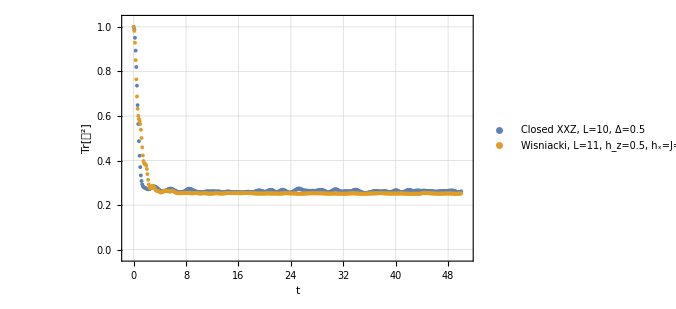

```mathematica
ListPlot[Transpose[{Range[t0,tf,Δt],#}]&/@{choiPurities,choiPuritiesWisniacki},
PlotRange->{{-0.8,50.8},{-0.03,1.03}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->22],
GridLines->Automatic,
ImageSize->500,
PlotLegends->Placed[LineLegend[{"Closed XXZ, "<>ToString[TraditionalForm[HoldForm[L=10]]]<>", "<>ToString[TraditionalForm[HoldForm[Δ=0.5]]],"Wisniacki, L=11, h_z=0.5, h_x=J=1"}],{Right,Top}],
LabelStyle->Directive[Black,FontSize->17]
]
```

Import data of Lipkin’s model:

```mathematica
superoperators=Import["../lipkin/vie_25_oct_2024_1.mx","MX"];
```

```mathematica
choisLipkin=1/2*Map[Reshuffle,superoperators,{2}];
```

```mathematica
choiPuritiesLipkin=Chop[Map[Purity,choisLipkin,{2}]];
```

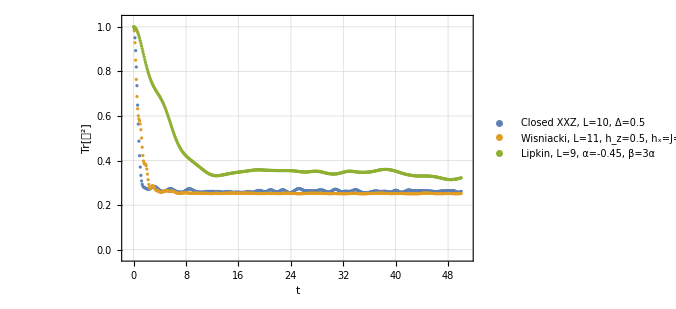

```mathematica
ListPlot[Transpose[{Range[t0,tf,Δt],#}]&/@{choiPurities,choiPuritiesWisniacki,choiPuritiesLipkin[[3]]},
PlotRange->{{-0.8,50.8},{-0.03,1.03}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->22],
GridLines->Automatic,
ImageSize->500,
PlotLegends->Placed[LineLegend[{"Closed XXZ, "<>ToString[TraditionalForm[HoldForm[L=10]]]<>", "<>ToString[TraditionalForm[HoldForm[Δ=0.5]]],"Wisniacki, L=11, h_z=0.5, h_x=J=1","Lipkin, L=9, α=-0.45, β=3α"}],{Right,Top}],
LabelStyle->Directive[Black,FontSize->17]
]
```

```mathematica
{Mean[#],StandardDeviation[#]}&[choiPurities[[40;;]]]
{Mean[#],StandardDeviation[#]}&[choiPuritiesWisniacki[[40;;]]]
{Mean[#],StandardDeviation[#]}&[choiPuritiesLipkin[[3]]]
```

{0.26284,0.0040504}

{0.252993+0. ⅈ,0.00231681}

{0.402152,0.145256}

## Checking spectrum

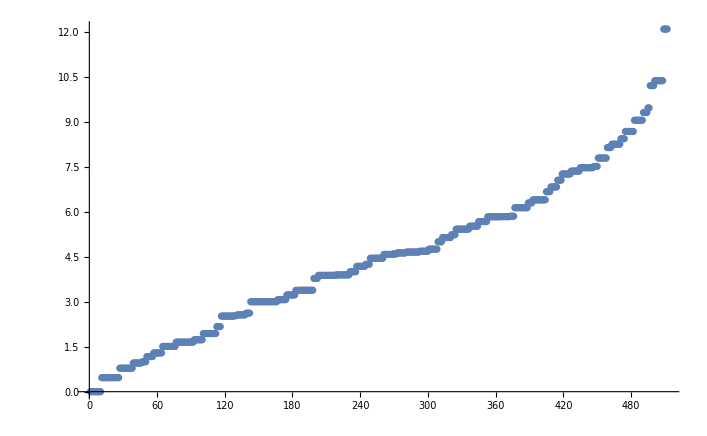

```mathematica
ListPlot[eigenvalsH]
```

```mathematica
?MeanLevelSpacingRatio
```

```mathematica
MeanLevelSpacingRatio[eigenvalsH]
```

Divide::indet: Indeterminate expression 0/0 encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

Divide::infy: Infinite expression 0.467911/0 encountered.

Divide::infy: Infinite expression (6.66134×10^-16)/0. encountered.

Divide::infy: Infinite expression (4.44089×10^-16)/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Indeterminate

## XXZ with defect (chaotic)

```mathematica
L=9;(* number of spins *)
Δ=0.5;(* anisotropy *)
```

Compute eigenvalues and eigenvectors of Hamiltonian:

```mathematica
H=ClosedXXZHamiltonian[L,Δ]+0.5Pauli[{0,0,0,0,0,3,0,0,0}];
```

```mathematica
{eigenvalsH,eigenvecsH}=Transpose[Sort[Transpose[Chop[Eigensystem[H]]]]];
```

```mathematica
ψE=RandomChainProductState[L-1];
```

```mathematica
t=Power[10,Range[-2,2,0.05]];
```

```mathematica
{t0,tf,Δt}={0,10,0.2};
t=Power[10,Range[-2,2,0.05]];
AbsoluteTiming[superoperators=Chop[Superoperator[#,ψE,eigenvalsH,eigenvecsH,L]]&/@t;]
```

{49.4879,Null}

```mathematica
chois=1/2*Reshuffle/@superoperators;
```

```mathematica
choiPurities=Chop[Purity/@chois];
```

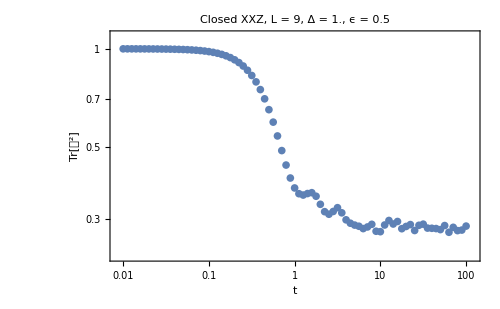

```mathematica
ListLogLogPlot[Transpose[{t,choiPurities}],
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->21],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,19],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Closed XXZ, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>", "<>ToString[TraditionalForm[HoldForm[Δ]]]<>" = "<>ToString[Δ]<>", ϵ = 0.5",
LabelStyle->Directive[Black,FontSize->17]
]
```

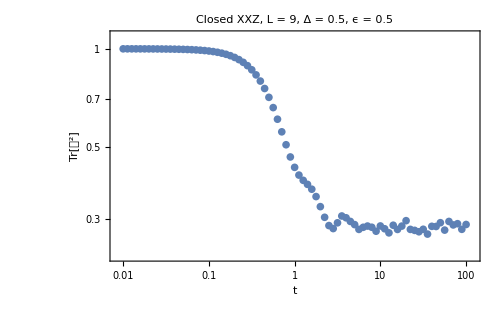

```mathematica
ListLogLogPlot[Transpose[{t,choiPurities}],
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->21],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,19],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Closed XXZ, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>", "<>ToString[TraditionalForm[HoldForm[Δ]]]<>" = "<>ToString[Δ]<>", ϵ = 0.5",
LabelStyle->Directive[Black,FontSize->17]
]
```

```mathematica
MatrixPartialTrace[1/4*IdentityMatrix[4],2,2]
```

{{1/2,0},{0,1/2}}

1/4(0,0|0,0+0,1|0,1+1,0|1,0+1,1|1,1)